# Práctica 4

### a) Definir la matriz de adyacencia del grafo G (sin peso)

```mathematica
g1 =FromAdjacencyMatrix[{
{0,1,1,0,0,0,0,0},
{1,0,1,1,0,0,0,0},
{1,1,0,1,1,0,0,0},
{0,1,1,0,1,1,0,0},
{0,0,1,1,0,0,1,0},
{0,0,0,1,0,0,1,1},
{0,0,0,0,1,1,0,1},
{0,0,0,0,0,1,1,0}}]
```

⁃Graph:<12,8,Undirected>⁃

### b) Expresa gráficamente

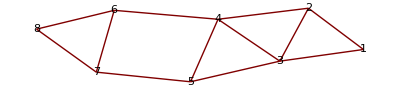

```mathematica
GraphPlot[g1,VertexLabeling->True]
```

### c) ¿Es euleriano? ¿Es regular?

```mathematica
RegularQ[g1]
```

False

```mathematica
EulerianQ[g1]
```

False

### d) Calcula el subgrafo que se obtiene eliminando el vértice E

```mathematica
g2=DeleteVertex[g1,5]
```

⁃Graph:<9,7,Undirected>⁃

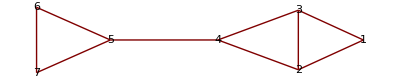

```mathematica
GraphPlot[g2,VertexLabeling->True]
```

### e) Calcula el grado de cada uno de los vértices del grafo G

```mathematica
Degrees[g1]
```

{2,3,4,4,3,3,3,2}

### f) ¿Es el grafo G un árbol?

```mathematica
TreeQ[g1]
```

False

### g) Define la matriz de adyacencia del grafo G considerando los pesos de los arcos

```mathematica
g3 =FromAdjacencyMatrix[{
{Infinity,4,3,Infinity,Infinity,Infinity,Infinity,Infinity},
{4,Infinity,2,5,Infinity,Infinity,Infinity,Infinity},
{3,2,Infinity,3,6,Infinity,Infinity,Infinity},
{Infinity,5,3,Infinity,1,5,Infinity,Infinity},
{Infinity,Infinity,6,1,Infinity,Infinity,5,Infinity},
{Infinity,Infinity,Infinity,5,Infinity,Infinity,2,7},
{Infinity,Infinity,Infinity,Infinity,5,2,Infinity,4},
{Infinity,Infinity,Infinity,Infinity,Infinity,4,7,Infinity}},EdgeWeight]
```

⁃Graph:<12,8,Undirected>⁃

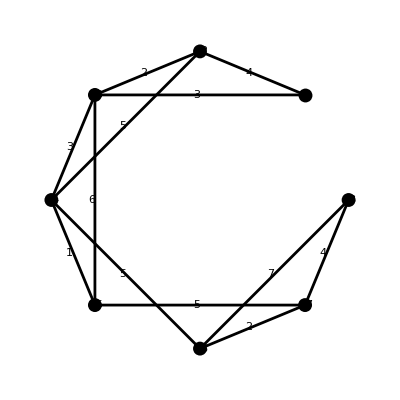

```mathematica
ShowGraph[SetEdgeLabels[g3,GetEdgeWeights[g3]],VertexLabel->True]
```

### h) Calcula la mínima distancia del vértice A a cada uno de los demás vértices

```mathematica
Dijkstra[g3,1]
```

{{1,1,1,3,4,4,5,7},{0,4,3,6,7,11,12,16}}

~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~
Interpretación :
  d (A, B) = 4  	A B
  d(A, C) = 3	A C
  d(A, D) = 6	A C D
  d(A, E) = 7	A C D E
  d(A, F) = 11	A C D F
  d(A, G) = 12	A C D E G 
  d(A, H) = 16	A C D E G H   
 ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~

### i) Calcula un árbol recubridor minimal del grafo G

```mathematica
g4=MinimumSpanningTree[g3]
```

⁃Graph:<7,8,Undirected>⁃

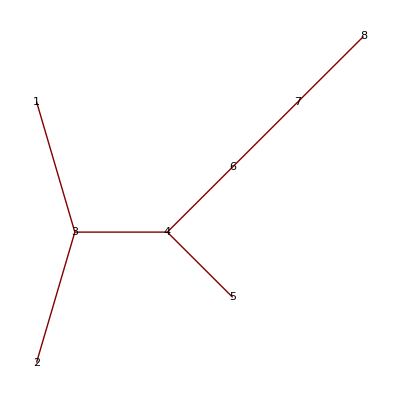

```mathematica
GraphPlot[g4,VertexLabeling->True]
```

#### Interpretación

### Peso del árbol minimal

```mathematica
3+2+3+1+5+2+4
```

20